# BOBby

```mathematica
Quit[]
```

```mathematica
NSolve[Sech[x/11.8]==0.1,x]
NSolve[Sech[x/11.2]==0.1,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-35.32},{x→35.32}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-33.5241},{x→33.5241}}

```mathematica
35.3200295842913*11.2/11.8
```

33.5241

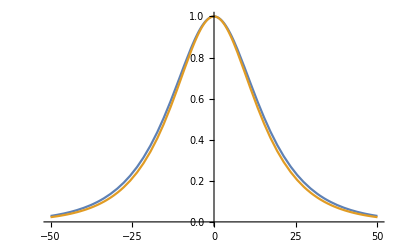

```mathematica
Plot[{Sech[x/11.8],Sech[x/11.2]},{x,-50,50}]
```

## Setup

* Some packages may not be available yet. I ll make them free in the near future.

### Read packages

```mathematica
<<NRMatch.m
<<BBHReduce.m
<<NRHybrids.m
<<NRUnits.m
<<PNParticles.m
<<NRWaves.m
<<NRFits.m
<<DataFits.m
<<PNApproximantsalignedspins.m
```

Get::noopen: Cannot open NinjaBase`.

Needs::nocont: Context NinjaBase` was not created when Needs was evaluated.

Import::nffil: File ~/SVN/WaveGearData/Detectors/H1L1-AVERAGE_PSD-1127271617-1027800.txt.gz not found during Import.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

UUID::shdw: Symbol UUID appears in multiple contexts {UUID`,NRFiles`}; definitions in context UUID` may shadow or be shadowed by other definitions.

Get::noopen: Cannot open NinjaBase`.

Needs::nocont: Context NinjaBase` was not created when Needs was evaluated.

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

η::shdw: Symbol η appears in multiple contexts {DataFits`,sym`}; definitions in context DataFits` may shadow or be shadowed by other definitions.

η::shdw: Symbol η appears in multiple contexts {PNStrain`,DataFits`,sym`}; definitions in context PNStrain` may shadow or be shadowed by other definitions.

η$::shdw: Symbol η$ appears in multiple contexts {PNStrain`,sym`}; definitions in context PNStrain` may shadow or be shadowed by other definitions.

MakeT1Xdot::shdw: Symbol MakeT1Xdot appears in multiple contexts {PNApproximantsalignedspins`,PNParticles`}; definitions in context PNApproximantsalignedspins` may shadow or be shadowed by other definitions.

MakeT4Xdot::shdw: Symbol MakeT4Xdot appears in multiple contexts {PNApproximantsalignedspins`,PNParticles`}; definitions in context PNApproximantsalignedspins` may shadow or be shadowed by other definitions.

### Load data

```mathematica
fitfile=NotebookDirectory[]<>"swsh_fits.dat"
fitfileSS=NotebookDirectory[]<>"swsh_alpha_fits.dat"
```

/Users/xisco/Work/AEI/BoB/swsh_fits.dat

/Users/xisco/Work/AEI/BoB/swsh_alpha_fits.dat

```mathematica
mixcoefits=Import[fitfile];
mixcoefitsSS=Import[fitfileSS];
```

```mathematica
(* Case to analyse *)
ind=3;
```

```mathematica
nruns=FileNames["*",datfol]
```

{}

```mathematica
files=FileNames["*",nruns[[ind]]]
```

Part::partw: Part 3 of {} does not exist.

Part::partw: Part 3 of Alternatives[] does not exist.

Part::partd: Part specification \b\B⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of Alternatives[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification \b\B⟦3⟧ is longer than depth of object.

{}

```mathematica
wavefls=(FileNames["*",files[[-1]]][[1;;7]]);
```

Part::partw: Part -1 of {} does not exist.

Part::partw: Part -1 of Alternatives[] does not exist.

Part::partd: Part specification \b\B⟦-1⟧ is longer than depth of object.

Part::partw: Part -1 of Alternatives[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification \b\B⟦-1⟧ is longer than depth of object.

Part::take: Cannot take positions 1 through 7 in {}.

```mathematica
waves=Import[#,"Table"]&/@wavefls;
```

Import::chtype: First argument {} is not a valid file, directory, or URL specification.

Import::chtype: First argument 1;;7 is not a valid file, directory, or URL specification.

Part::pkspec1: The expression $Failed cannot be used as a part specification.

### PN scalar-field

```mathematica
dEdΩ[Ω_,q_]:=Evaluate[-4/3 Ω^(-1/3) (1+q)^2/q]
```

```mathematica
dΩ2[dΩ0_,dE0_,dE2_,Ω0_,q_]:=dΩ0/dE0(dE2-dΩ0*(-(4 (1+q)^2)/(3 q Ω0^(1/3))))
```

```mathematica
PNSGBSF[m1_,m2_,αGB_,ω_,OptionsPattern[{"Orientation"->{0,0},"ExtRadius"->100,"m"->-1}]]:=Block[{Φ0,Φ1,Φ2,Φ3,Φ4,M,orient,θ,φ,b,R,sol,m},
orient=OptionValue["Orientation"];
R=OptionValue["ExtRadius"];
m=OptionValue["m"];

{θ,φ}=orient;
If[m1+m2>1,Print["masses must be normalized to 1"];Return[];];

M=1;
b=(ω^(-2) )^(1/3);
Φ0=(M αGB)/((m1 m2) (2 R));
Φ1=((b(m2-m1) ω Sin[θ] Sin[φ-ω t])αGB)/((m1 m2) (2 R));
Φ2=-((b^2 ω^2 Sin[θ]^2 (m1^2-m1 m2+m2^2)Cos[2φ-2 t ω])αGB)/((m1 m2 M) (2 R));
Φ3=((b^3 ω^3 Sin[θ]^3 (m1-m2) (m1^2+m2^2) (Sin[φ-t ω]+9 Sin[3 φ-3 t ω]))αGB)/((8 m1 m2 M^2) (2 R));

Φ4=1/((3 m1 m2 M^3) (2 R))(b^4 ω^4 Sin[θ]^4 (m1^4-m1^3 m2+m1^2 m2^2-m1 m2^3+m2^4) (Cos[2 φ-2 t ω]+4 Cos[4 φ-4 t ω]))αGB;
sol=Φ0+Φ1+Φ2+Φ3+Φ4;

Which[m==-1,sol;,m==0,sol=Φ0;,m==1,sol=Φ1;,m==2,sol=Φ2;,m==3,sol=Φ3;,m==4,sol=Φ4;];

(* This factor 4 has to do with the redefinition of αGB. See eq. A2 of 1810.05177.pdf *)
4 sol
]
```

## Psi4 peak

### Dirty shit

```mathematica
sxsdir="/Users/xisco/SXS";
sxsdirs=Select[FileNames["*q*",sxsdir],DirectoryQ[#]&];
```

```mathematica
<<BBHReduce.m
mysxscase=SXSParClassification[sxsdirs,{{"Non-Precessing"},{"χ1","-0.02<#<0.02"},{"χ2","-0.02<#<0.02"}}]
modes={{2,2}}
```

Get::noopen: Cannot open NinjaBase`.

Needs::nocont: Context NinjaBase` was not created when Needs was evaluated.

Classification Input Variables. Examples: {{'MassRatio', '0.99<#<1.1'}},{{'Distance', '#>16'}},{{'Orbits', '#>25'}},{{'Precessing'}},
{{'Non-Precessing'}},{{'High-Spin'}},{{'χeff','#>0.6'}},{{'χ1','#>0.6'}},{{'χ2','#>0.6'}},{{'Unequal'}}

Take care! Some of the sxs file names are not consistent with the metadata files

The spin definition is consitent with 'initial-spin' values and not relaxed ones

The mass definition is consitent with 'initial-mass' values and not relaxed ones

{/Users/xisco/SXS/BBH_SKS_d23.1_q1_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/d13_q2_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/d14.0_q3.0_s0_0_0_s0_0_0,/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/BBH_CFMS_d11.4_q9_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/BBH_CFMS_d13_q10_sA_0_0_0_sB_0_0_0}

{{2,2}}

```mathematica
mysxscaserh=(FileNames["rM*",#,2]&/@mysxscase)[[All,1]]
mysxscasemetafile=Flatten[FileNames["metadata.txt",#,2]&/@mysxscase]
metadata=SXSMetaFilesToRules[mysxscasemetafile];
```

{/Users/xisco/SXS/BBH_SKS_d23.1_q1_sA_0_0_0_sB_0_0_0/Lev4/rMPsi4_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/d13_q2_sA_0_0_0_sB_0_0_0/Lev5/rMPsi4_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/d14.0_q3.0_s0_0_0_s0_0_0/Lev5/rMPsi4_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0/Lev4/rMPsi4_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0/Lev4/rMPsi4_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/BBH_CFMS_d11.4_q9_sA_0_0_0_sB_0_0_0/Lev5/rMPsi4_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/BBH_CFMS_d13_q10_sA_0_0_0_sB_0_0_0/Lev4/rMPsi4_Asymptotic_GeometricUnits_CoM.h5}

{/Users/xisco/SXS/BBH_SKS_d23.1_q1_sA_0_0_0_sB_0_0_0/Lev4/metadata.txt,/Users/xisco/SXS/d13_q2_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/d14.0_q3.0_s0_0_0_s0_0_0/Lev5/metadata.txt,/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0/Lev2/metadata.txt,/Users/xisco/SXS/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0/Lev4/metadata.txt,/Users/xisco/SXS/BBH_CFMS_d11.4_q9_sA_0_0_0_sB_0_0_0/Lev5/metadata.txt,/Users/xisco/SXS/BBH_CFMS_d13_q10_sA_0_0_0_sB_0_0_0/Lev5/metadata.txt}

```mathematica
mysxscasemetadata=SXSMetaFilesToRules/@mysxscasemetafile;
Print["mass1 = ",mass1=Flatten[("initial-mass1"/.mysxscasemetadata)]]
Print["mass2 = ",mass2=Flatten[("initial-mass2"/.mysxscasemetadata)]]
Print["χ1 = ",χ1=Chop[(("initial-dimensionless-spin1"/.mysxscasemetadata)),10^-6][[All,-1]]]
Print["χ2 = ",χ2=Chop[(("initial-dimensionless-spin2"/.mysxscasemetadata)),10^-6][[All,-1]]]
Print["m1/m2 = ",qt=mass1/mass2]
Print["m1·m2 = ",ηt=q/(1+qt)^2*1.]
```

mass1 = {0.5,0.666667,0.75,0.8,0.857144,0.9,0.909091}

mass2 = {0.5,0.333333,0.25,0.2,0.142858,0.1,0.0909091}

χ1 = {0,0,0,0,0,0,0}

χ2 = {0,0,0,0,0,0,0}

m1/m2 = {1.,2.,3.,4.,5.99997,9.,10.}

m1·m2 = {0.25 q,0.111111 q,0.0625 q,0.04 q,0.0204084 q,0.01 q,0.00826446 q}

```mathematica
sxsrhs=Flatten[GetAsymptoticMultiMode[#,4,modes,"ReSample"->True]&/@mysxscaserh,1];
```

```mathematica
ValueOfMaximum/@sxsrhs
```

{0.0721725,0.0593383,0.0446037,0.0348414,0.0238257,0.0168039,0.0144695}

```mathematica
data=Transpose[{qt,ValueOfMaximum/@sxsrhs}];
```

```mathematica
nsInitAnsatzList=Generate1DPolynomialAnsatz["a",η,5,5]/. a0-> 0
nsInitAnsatz=nsInitAnsatzList[[1,1]]
```

{{a1 η+a2 η^2+a3 η^3+a4 η^4+a5 η^5,{η}}}

a1 η+a2 η^2+a3 η^3+a4 η^4+a5 η^5

```mathematica
fits=DataFitFunction[data,nsInitAnsatzList];
```

0.121449 η-0.0689221 η^2+0.0150079 η^3-0.00142457 η^4+0.0000493037 η^5 | 5 | 0.990725 | 4.14904×10^-3 | 18.8462 | -41.4784 |  | Estimate | Standard Error | t-Statistic | P-Value
a1 | 0.121449 | 0.0156708 | 7.75007 | 0.0162445
a2 | -0.0689221 | 0.0128851 | -5.34899 | 0.033219
a3 | 0.0150079 | 0.00360194 | 4.16661 | 0.0530587
a4 | -0.00142457 | 0.000410674 | -3.46885 | 0.073999
a5 | 0.0000493037 | 0.0000164278 | 3.00124 | 0.0953981

```mathematica
nsAnsatzList = Generate1DPolynomialAnsatz["a",η,2,7]/. a0-> 0
```

{{a1 η+a2 η^2,{η}},{a1 η+a2 η^2+a3 η^3,{η}},{a1 η+a2 η^2+a3 η^3+a4 η^4,{η}},{a1 η+a2 η^2+a3 η^3+a4 η^4+a5 η^5,{η}},{a1 η+a2 η^2+a3 η^3+a4 η^4+a5 η^5+a6 η^6,{η}},{a1 η+a2 η^2+a3 η^3+a4 η^4+a5 η^5+a6 η^6+a7 η^7,{η}}}

```mathematica
nsInitCoeffRules=fits[[1,2]]
```

{a1→0.121449,a2→-0.0689221,a3→0.0150079,a4→-0.00142457,a5→0.0000493037}

```mathematica
nsPadeList   = Generate1DPadeAnsatzList[nsInitAnsatz,nsInitCoeffRules,η,"a",1,6]
nsAnsatzList = Join[nsAnsatzList,nsPadeList];
```

Not generating Pade approximant for type (5,1) with polynomial ansatz of order 5, as it would just duplicate the polynomial.

Generated these Pade approximants:

{{(0.121 a1 η)/(1+0.567 a3 η),{η}},{(0.121 a1 η-0.0425 a2 η^2)/(1+0.218 a4 η),{η}},{(0.121 a1 η-0.0332 a2 η^2)/(1+0.294 a4 η+0.0434 a5 η^2),{η}},{(0.121 a1 η-0.0574 a2 η^2+0.00847 a3 η^3)/(1+0.0949 a5 η),{η}},{(0.121 a1 η-0.0517 a2 η^2+0.00649 a3 η^3)/(1+0.142 a5 η+0.0101 a6 η^2),{η}},{(0.121 a1 η-0.0485 a2 η^2+0.0056 a3 η^3)/(1+0.168 a5 η+0.018 a6 η^2+0.00115 a7 η^3),{η}},{(0.121 a1 η-0.0647 a2 η^2+0.0126 a3 η^3-0.000905 a4 η^4)/(1+0.0346 a6 η),{η}},{(0.121 a1 η-0.0623 a2 η^2+0.0115 a3 η^3-0.000737 a4 η^4)/(1+0.0545 a6 η+0.00189 a7 η^2),{η}}}

{{(0.121 a1 η)/(1+0.567 a3 η),{η}},{(0.121 a1 η-0.0425 a2 η^2)/(1+0.218 a4 η),{η}},{(0.121 a1 η-0.0332 a2 η^2)/(1+0.294 a4 η+0.0434 a5 η^2),{η}},{(0.121 a1 η-0.0574 a2 η^2+0.00847 a3 η^3)/(1+0.0949 a5 η),{η}},{(0.121 a1 η-0.0517 a2 η^2+0.00649 a3 η^3)/(1+0.142 a5 η+0.0101 a6 η^2),{η}},{(0.121 a1 η-0.0485 a2 η^2+0.0056 a3 η^3)/(1+0.168 a5 η+0.018 a6 η^2+0.00115 a7 η^3),{η}},{(0.121 a1 η-0.0647 a2 η^2+0.0126 a3 η^3-0.000905 a4 η^4)/(1+0.0346 a6 η),{η}},{(0.121 a1 η-0.0623 a2 η^2+0.0115 a3 η^3-0.000737 a4 η^4)/(1+0.0545 a6 η+0.00189 a7 η^2),{η}}}

```mathematica
fits=DataFitFunction[data,nsPadeList];
```

Power::infy: Infinite expression 1/0 encountered.

(0.245611 η-0.0540368 η^2+0.00701081 η^3-0.000313801 η^4)/(1+1.24387 η+0.503142 η^2) | 6 | 0.999994 | 1.02299×10^-4 | ComplexInfinity | -87.5186 |  | Estimate | Standard Error | t-Statistic | P-Value
a1 | 2.02984 | 0.51262 | 3.95974 | 0.15748
a2 | 0.867364 | 0.38178 | 2.2719 | 0.263969
a3 | 0.609635 | 0.253465 | 2.40521 | 0.250843
a4 | 0.425781 | 0.171869 | 2.47736 | 0.244242
a6 | 22.8233 | 12.9582 | 1.7613 | 0.328736
a7 | 266.213 | 80.6839 | 3.29945 | 0.187345
(0.123594 η+0.000568639 η^2)/(1-0.159946 η+0.880384 η^2) | 4 | 0.999973 | 2.24823×10^-4 | -65.8065 | -86.077 |  | Estimate | Standard Error | t-Statistic | P-Value
a1 | 1.02144 | 0.0997228 | 10.2427 | 0.00198389
a2 | -0.0171277 | 0.0217533 | -0.78736 | 0.488546
a4 | -0.544033 | 0.421038 | -1.29212 | 0.286847
a5 | 20.2853 | 0.864378 | 23.4681 | 0.000169513
(0.123484 η+0.000593673 η^2-1.53788×10^-6 η^3)/(1-0.161213 η+0.880457 η^2) | 5 | 0.999973 | 2.24822×10^-4 | -21.9683 | -82.2929 |  | Estimate | Standard Error | t-Statistic | P-Value
a1 | 1.02053 | 0.309467 | 3.2977 | 0.0809471
a2 | -0.011483 | 0.152192 | -0.0754512 | 0.946724
a3 | -0.000236962 | 0.0738952 | -0.00320673 | 0.997733
a5 | -1.1353 | 2.99436 | -0.379146 | 0.741048
a6 | 87.174 | 5.06304 | 17.2177 | 0.00335628
(1.25864×10^10 η+4.28621×10^10 η^2+4.13325×10^8 η^3)/(1+5.19216×10^11 η-7.30099×10^10 η^2+3.27803×10^11 η^3) | 6 | 0.999973 | 2.22061×10^-4 | ComplexInfinity | -76.6679 |  | Estimate | Standard Error | t-Statistic | P-Value
a1 | 1.04019×10^11 | 6.80994×10^11 | 0.152746 | 0.903504
a2 | -8.83755×10^11 | 4.33941×10^11 | -2.03658 | 0.290577
a3 | 7.38081×10^10 | 2.47124×10^11 | 0.298668 | 0.815231
a5 | 3.09057×10^12 | 5.71661×10^12 | 0.540631 | 0.684478
a6 | -4.05611×10^12 | 6.67309×10^12 | -0.60783 | 0.652306
a7 | 2.85046×10^14 | 1.44783×10^11 | 1968.78 | 0.000323358
(0.53467 η-0.153286 η^2+0.0184038 η^3-0.000776405 η^4)/(1+4.52149 η) | 5 | 0.999922 | 3.81067×10^-4 | -14.581 | -74.9056 |  | Estimate | Standard Error | t-Statistic | P-Value
a1 | 4.41876 | 1.25163 | 3.53041 | 0.0717092
a2 | 2.36918 | 0.557878 | 4.24677 | 0.0512245
a3 | 1.46062 | 0.302153 | 4.83405 | 0.0402289
a4 | 0.857906 | 0.167802 | 5.11259 | 0.0361933
a6 | 130.679 | 46.9913 | 2.78092 | 0.108639
(4.4624×10^13 η-8.37378×10^12 η^2+4.73943×10^11 η^3)/(1+5.12486×10^14 η) | 4 | 0.99874 | 1.52917×10^-3 | -38.9662 | -59.2366 |  | Estimate | Standard Error | t-Statistic | P-Value
a1 | 3.68793×10^14 | 1.25777×10^13 | 29.3212 | 0.0000871186
a2 | 1.45885×10^14 | 1.2207×10^13 | 11.9509 | 0.00126016
a3 | 5.59555×10^13 | 7.21087×10^12 | 7.75987 | 0.00445178
a5 | 5.40027×10^15 | 1.23462×10^12 | 4374.04 | 2.63525×10^-11
(1.32651×10^14 η-1.16326×10^13 η^2)/(1+1.9598×10^15 η) | 3 | 0.973534 | 7.00882×10^-3 | -32.6658 | -40.8821 |  | Estimate | Standard Error | t-Statistic | P-Value
a1 | 1.09629×10^15 | 1.03435×10^14 | 10.5988 | 0.000448518
a2 | 2.73708×10^14 | 5.00182×10^13 | 5.47218 | 0.00542648
a4 | 8.98989×10^15 | 1.39159×10^13 | 646.018 | 3.44482×10^-11
(9.03042×10^13 η)/(1+2.37594×10^15 η) | 2 | 0.778296 | 2.02856×10^-2 | -25.3494 | -28.5116 |  | Estimate | Standard Error | t-Statistic | P-Value
a1 | 7.46316×10^14 | 1.72659×10^14 | 4.32248 | 0.00755288
a3 | 4.19036×10^15 | 3.07511×10^13 | 136.267 | 4.03739×10^-10

```mathematica
modelamp=fits[[2,1]]
```

(0.123594 η+0.000568639 η^2)/(1-0.159946 η+0.880384 η^2)

```mathematica
Clear[myfit]
```

```mathematica
fits[[1,1]]
```

(0.245611 η-0.0540368 η^2+0.00701081 η^3-0.000313801 η^4)/(1+1.24387 η+0.503142 η^2)

```mathematica
myfit[η_]:=Evaluate[fits[[2,1]]]
```

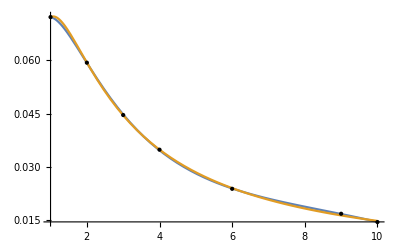

```mathematica
Plot[{fits[[1,1]],fits[[2,1]]},{η,1,10},Epilog->{Point[data]}]
```

```mathematica
tmaxs=TimeOfMaximum/@sxsrhs
```

{25491.1,3738.24,4472.23,7201.71,6596.58,3701.39,7035.98}

```mathematica
data=Table[Select[Abs0DStructs@sxsrhs[[i]],tmaxs[[i]]-20≤ #[[1]]≤tmaxs[[i]]+100&]/.{xx_,yy_}->{xx-tmaxs[[i]],yy},{i,Length@sxsrhs}];
```

```mathematica
ansatz=(A) 1/Cosh[γ (t-tp)];
```

```mathematica
modelswA=Table[NonlinearModelFit[data[[i]],(A) 1Sech[γ (t-tp)],{{A,0.001},γ,tp},t],{i,Length@data}];
```

```mathematica
modelswAf=Table[NonlinearModelFit[data[[i]],( (myfit[η]/.η->qt[[i]])) 1Sech[γ (t-tp)],{γ,tp},t],{i,Length@data}];
```

```mathematica
modelswAf[[1]]["BestFitParameters"]
modelswA[[1]]["BestFitParameters"]
```

{γ→-0.0863338,tp→0.785466}

{A→0.0728416,γ→0.0870879,tp→0.795766}

```mathematica
modelswAf[[-1]]["BestFitParameters"]
modelswA[[-1]]["BestFitParameters"]
```

{γ→-0.0893311,tp→-0.194045}

{A→0.0143402,γ→0.0867053,tp→-0.244313}

```mathematica
modelswAf[[4]]["BestFitParameters"]
modelswA[[4]]["BestFitParameters"]
```

{γ→-0.0892396,tp→-0.171412}

{A→0.0345419,γ→0.0884706,tp→-0.184019}

```mathematica
modelswAn=Normal/@modelswA;
modelswAfn=Normal/@modelswAf;
```

```mathematica
FindRoot[Sech[0.08933105238986211 (t)]==0.1,{t,-20}]
FindRoot[Sech[0.08633380440129493 (t)]==0.1,{t,-20}]
```

{t→-33.5071}

{t→-34.6703}

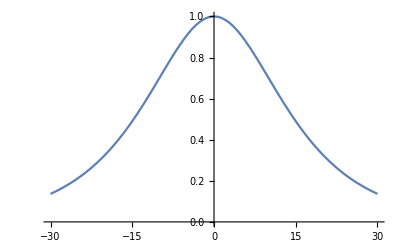

```mathematica
Plot[Sech[0.08933105238986211 (t)],{t,-30,30}]
```

```mathematica
NIntegrate[0.5Sech[0.08933105238986211 (t)],{t,-40,40}]
```

16.9558

```mathematica
fr[q_]:=(0.8q^3-2.6q^2+2.8q +1)/(π 6)^(3/2)
```

```mathematica
fr[1]/fr[10]*(0.07284161283530767)/(0.01434022671468842)
```

0.0178542

```mathematica
af=FinalSpinUIB2017[0.25,0,0];
mf=1-EradUIB2017[0.25,0,0];
```

```mathematica
fr[1]
```

0.0244387

```mathematica
FindRoot[π fr[1]==mf^0.5/(r^(3/2)-af mf^0.5),{r,8}]
```

{r→5.63464}

```mathematica
phi=Interpolation@Arg0DStructs@Conjugate@sxsrhs[[-1]]
frq1=D[phi@t,t]
```

InterpolatingFunction[…]

InterpolatingFunction[…][t]

```mathematica
fr[10]
```

6.95281

```mathematica
TimeOfMaximum[sxsrhs[[1]]]
```

25491.1

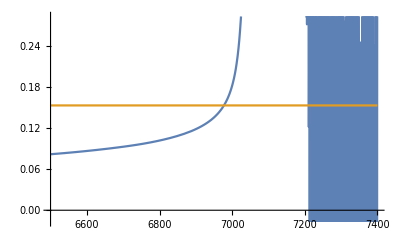

```mathematica
Plot[{frq1,fr[1]*2π},{t,6500,7400}]
```

```mathematica
Ti
```

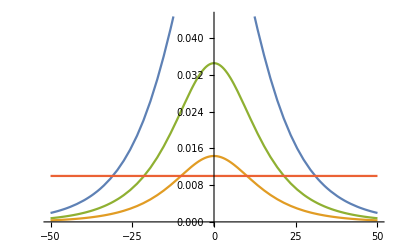

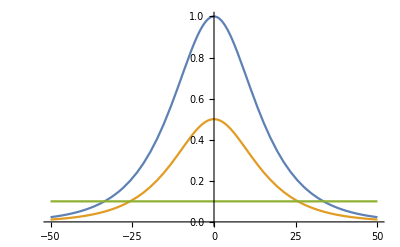

```mathematica
Plot[{(0.07284161283530767)Sech[0.08633380440129493 (t)],(0.01434022671468842)Sech[0.08933105238986211 (t)],0.03454189753881675Sech[0.08933105238986211 (t)],0.01},{t,-50,50}]
Plot[{Sech[0.08933105238986211 (t)],0.5Sech[0.08933105238986211 (t)],0.1},{t,-50,50}]
```

```mathematica
modelswAnb=#["SinglePredictionBands"]&/@modelswA;
modelswAnfb=#["SinglePredictionBands"]&/@modelswAf;
```

```mathematica
Plot[1/Cosh[1/0.000000000001x],{x,-20,80}]
```

```mathematica
Exp[-4.]
```

0.0183156

```mathematica
(* Not a huge difference between fitted version or not fitted one *)
```

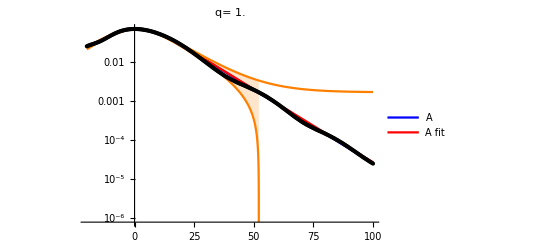
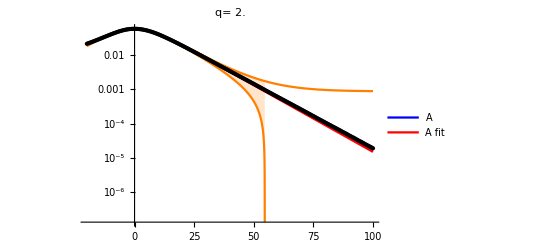
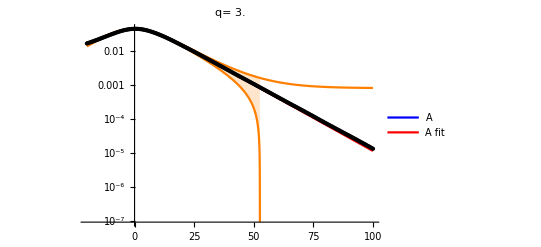
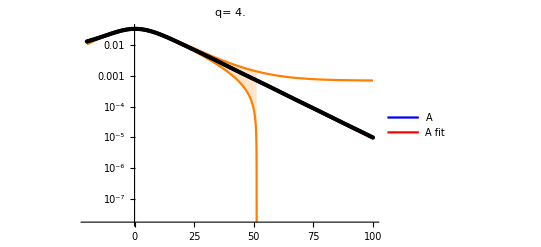
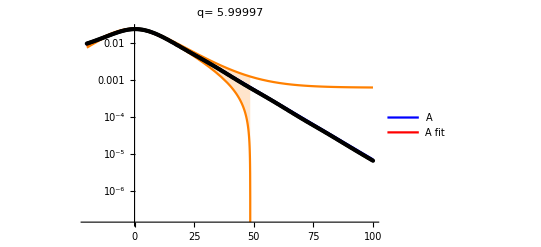
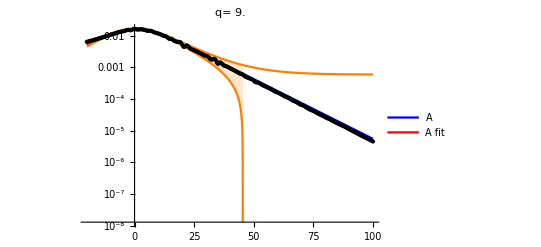
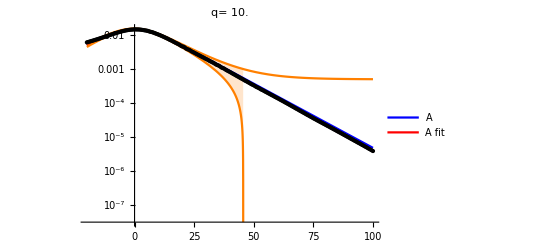

```mathematica
Table[LogPlot[{modelswAn[[i]],modelswAfn[[i]],modelswAnfb[[i,1]],modelswAnfb[[i,2]]},{t,-20,100},PlotLabel->"q= "<>ToString[qt[[i]]],PlotLegends->{"A","A fit"},PlotStyle->{Blue,Red,Orange,Orange},Filling->{3->{4}},Epilog->{Point[data[[i]]/.{xx_,yy_}->{xx,Log[yy]}]}],{i,Length@modelswAf}]
```

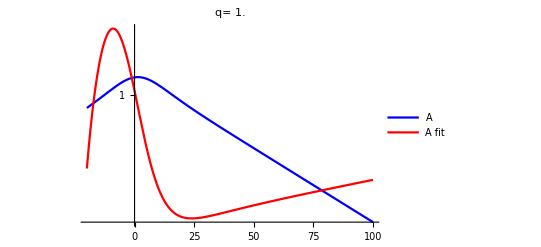
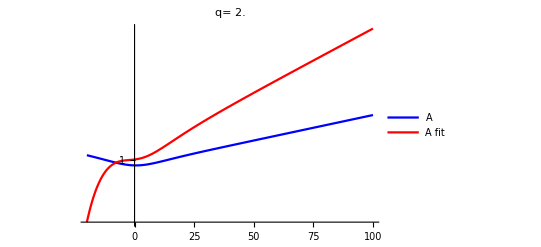
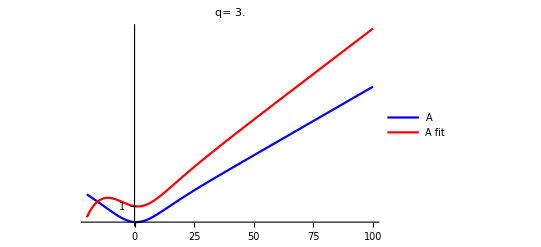
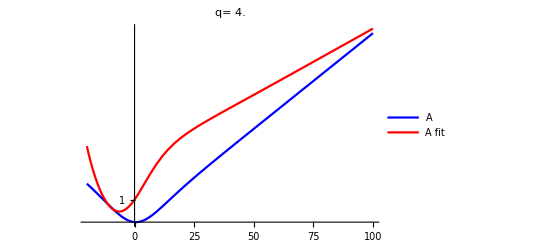
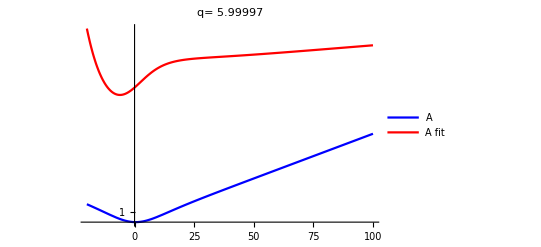
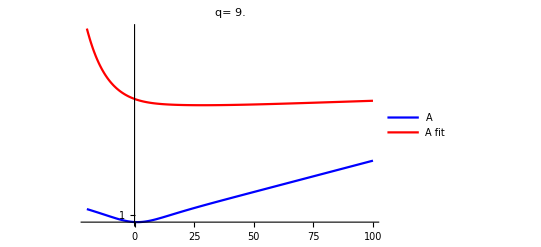
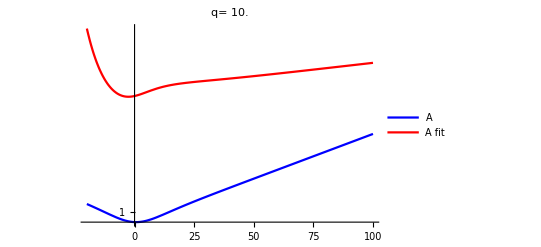

```mathematica
Table[LogPlot[{modelswAn[[i]]/modelswAfn[[i]],modelγ[myfit[i],γs[[i]],1/(ωrdown[2,2,0,Min[qt[[i]]/(1+qt[[i]])^2,qt[[i]]],0,0][[2]]),(ωrdown[2,2,0,Min[qt[[i]]/(1+qt[[i]])^2,qt[[i]]],0,0][[2]])]/modelswAfn[[i]]},{t,-20,100},PlotLabel->"q= "<>ToString[qt[[i]]],PlotLegends->{"A","A fit"},PlotStyle->{Blue,Red,Orange,Orange},Filling->{3->{4}}],{i,Length@modelswAf}]
```

```mathematica
lmnf1f2f3q1q2q3=Select[Import["/Users/xisco/Work/INFN/Work/Rdown//fitcoeffsWEB.dat"],UnsameQ[#,{}]&];
```

```mathematica
ωrdown[l_,m_,n_,η_,χ1_,χ2_]:=Module[{f1,f2,f3,q1,q2,q3,wr,q,τ},

{f1,f2,f3}=Select[lmnf1f2f3q1q2q3,#[[1]]==l&&#[[2]]==m&&#[[3]]==n&][[1,4;;6]];
{q1,q2,q3}=Select[lmnf1f2f3q1q2q3,#[[1]]==l&&#[[2]]==m&&#[[3]]==n&][[1,7;;9]];

(* Notice the factor 1/M ! *)
wr=1/(1-EradUIB2017[η,χ1,χ2])(f1+f2(1-FinalSpinUIB2017[η,χ1,χ2])^f3);
(*wr=(f1+f2(1-FinalSpinUIB2017[η,χ1,χ2])^f3);*)
(*q=1/(1-EradUIB2017[η,χ1,χ2])(q1+q2(1-FinalSpinUIB2017[η,χ1,χ2])^q3);*)
q=(q1+q2(1-FinalSpinUIB2017[η,χ1,χ2])^q3);

(* Notice the factor M ! *)
τ=1/(wr/(2 q))*1/(1-EradUIB2017[η,χ1,χ2]);
{wr,τ(1-EradUIB2017[η,χ1,χ2])}
]
```

```mathematica
ψ4mod[A_,γ_]:=A Sech[γ (t)]
```

```mathematica
γs=Abs[γ/.#["BestFitParameters"]&/@modelswA]
```

{0.0870879,0.0887931,0.0886204,0.0884706,0.0878574,0.0867935,0.0867053}

```mathematica
ωrdown[2,2,0,0.25,0,0]
ωrdown[2,2,0,0.2222,0,0]
```

{0.556174,11.6163}

{0.525797,11.4469}

```mathematica
γmod[γf_,γth_,τ_]:=(γf-γth)Exp[-t/τ]+γth
```

```mathematica
modelγ[A_,γf_,γth_,τ_]:=(A) 1/Cosh[γmod[γf,γth,τ] (t)]
```

```mathematica
modelγ[myfit[1],γs[[1]],1/(ωrdown[2,2,0,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[2]]),(ωrdown[2,2,1,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[2]])]
```

0.072169 Sech[(0.0883189-0.00123101 ⅇ^(-0.269397 t)) t]

```mathematica
τs=Chop@Table[1/(ωrdown[2,2,0,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[2]]),{ind,Length@qt}]
ws=Chop@Table[(ωrdown[2,2,0,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[1]]),{ind,Length@qt}]
```

{0.0860861,0.0873592,0.0883189,0.0887041,0.0888187,0.0886104,0.0885293}

{0.556174,0.525819,0.493069,0.470217,0.442335,0.42064,0.415977}

```mathematica
1/τs[[1]]/(1/τs[[-1]])
```

1.02838

General::munfl: Sech[-1.58276×10^99] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Sech[-1.82849×10^87] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

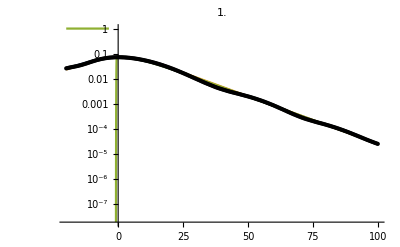
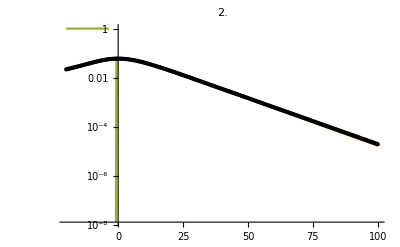
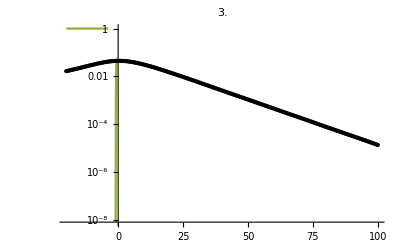
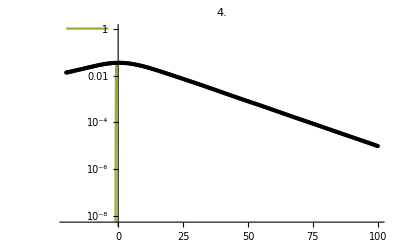
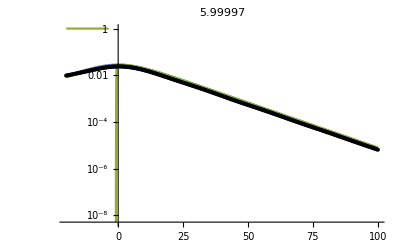
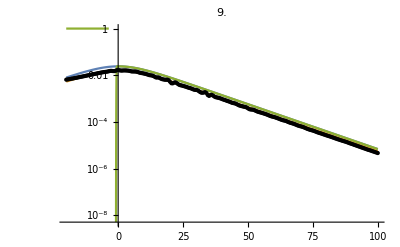
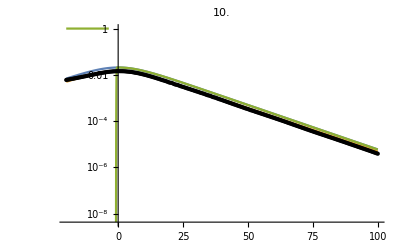

```mathematica
Table[LogPlot[{ψ4mod[myfit[ind],τs[[ind]]],modelswAn[[ind]],modelγ[myfit[ind],γs[[ind]],τs[[ind]],τs[[ind]]]},{t,-20,100},Epilog->Point[data[[ind]]/.{xx_,yy_}->{xx,Log[yy]}],PlotLabel->qt[[ind]]],{ind,Length@modelswAf}]
```

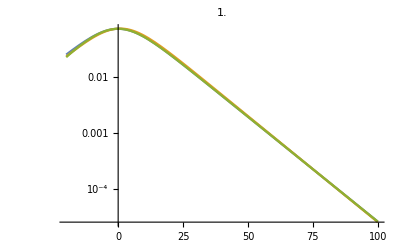
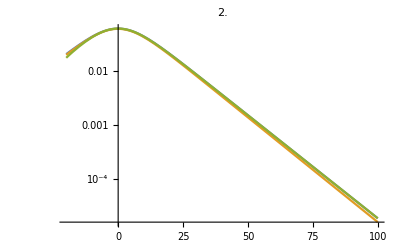
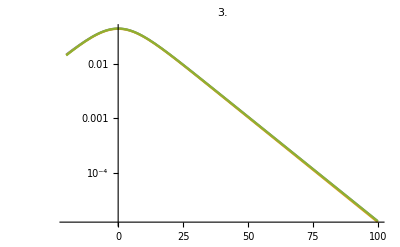
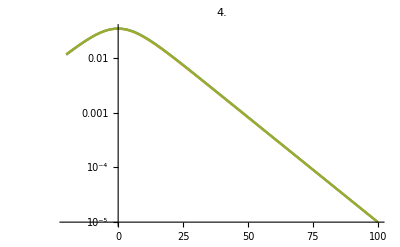
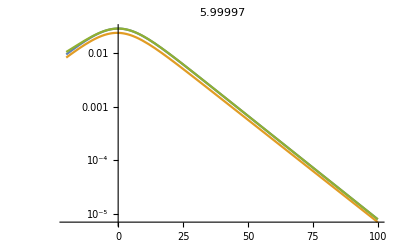
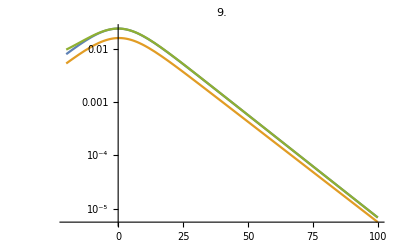
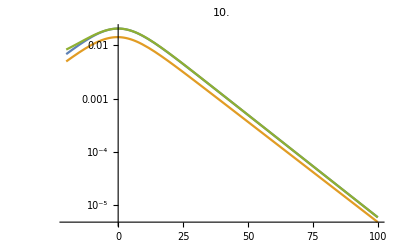

```mathematica
Table[LogPlot[{ψ4mod[myfit[ind],1/(ωrdown[2,2,0,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[2]])],modelswAn[[ind]],modelγ[myfit[ind],γs[[ind]],1/(ωrdown[2,2,0,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[2]]),(ωrdown[2,2,0,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[2]])]},{t,-20,100},PlotLabel->qt[[ind]]],{ind,Length@modelswAf}]
```

```mathematica
model=ψ4mod[myfit[ind],1/(ωrdown[2,2,0,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[2]])]
```

0.0445187 Sech[0.0883189 t]

```mathematica
res1=Transpose[{data[[1,All,1]],((model/.t->data[[1,All,1]])-data[[1,All,2]])}];
```

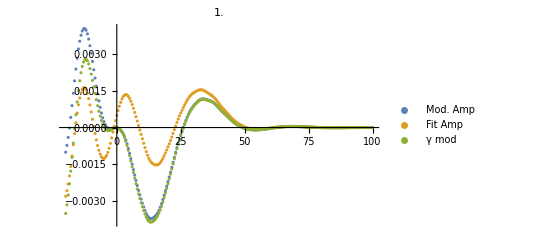
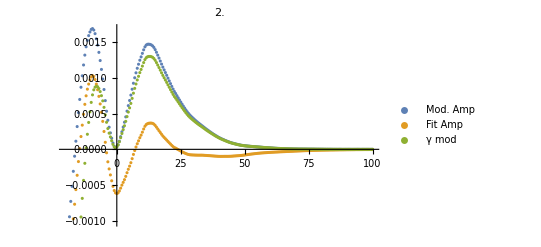
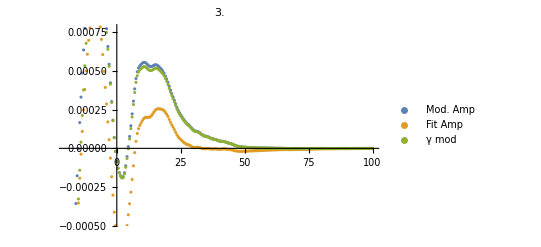
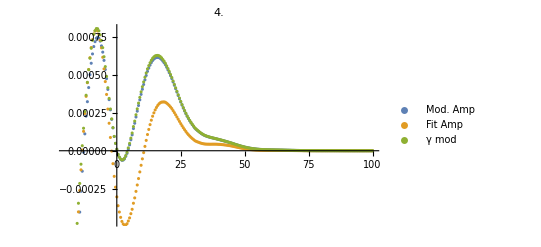
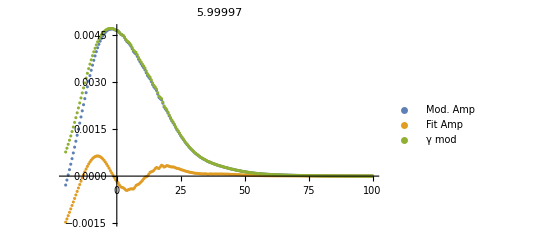
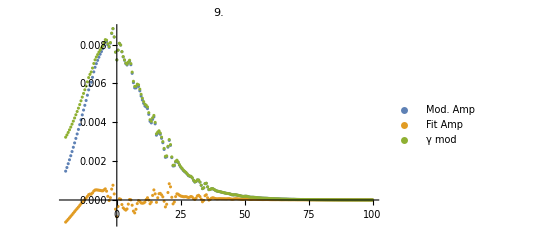
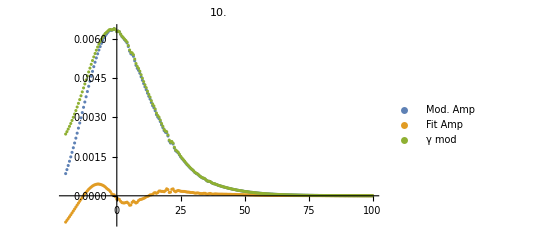

```mathematica
Table[ListPlot[{Transpose[{data[[ind,All,1]],((ψ4mod[myfit[ind],1/(ωrdown[2,2,0,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[2]])]/.t->data[[ind,All,1]])-data[[ind,All,2]])}],Transpose[{data[[ind,All,1]],((modelswAn[[ind]]/.t->data[[ind,All,1]])-data[[ind,All,2]])}],Transpose[{data[[ind,All,1]],((modelγ[myfit[ind],γs[[ind]],1/(ωrdown[2,2,0,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[2]]),(ωrdown[2,2,0,Min[qt[[ind]]/(1+qt[[ind]])^2,qt[[ind]]],0,0][[2]])]/.t->data[[ind,All,1]])-data[[ind,All,2]])}]},PlotLabel->qt[[ind]],PlotLegends->{"Mod. Amp","Fit Amp","γ mod"}],{ind,Length@modelswAf}]
```

### Dirty shit 2

## Mode Mixing

```mathematica
<<PNStrain.m
DefineYlms[2,6];
```

```mathematica
ModeMixingFitCoeffSY[η_,χ1_,χ2_,m_,l_,lp_,n_]:=Module[{im,p1r,p2r,p3r,p4r,p1i,p2i,p3i,p4i,re, χf,line},

χf=FinalSpinUIB2017[η,χ1,χ2];
(* the np+1 is just notation? *)
line=Select[mixcoefits,#[[1]]==m&&#[[2]]==l&&#[[3]]==lp&&#[[4]]==n &];
{p1r,p2r,p3r,p4r}=line[[1,5;;8]];
{p1i,p2i,p3i,p4i}=line[[1,9;;12]];

re=DiracDelta[l,lp]+p1r χf^(p2r)+p3r χf^(p4r);
im=p1i χf^(p2i)+p3i χf^(p4i);

re+I im
]
```

```mathematica
ModeMixingFitCoeffSYNorm[η_,χ1_,χ2_,m_,l_,lp_,n_,np_]:=Module[{im,norm,p1r,p2r,p3r,p4r,p1i,p2i,p3i,p4i,re, χf,line},

χf=FinalSpinUIB2017[η,χ1,χ2];
(* the np+1 is just notation? *)
line=Select[mixcoefits,#[[1]]==m&&#[[2]]==l&&#[[3]]==lp&&#[[4]]==n &];
{p1r,p2r,p3r,p4r}=line[[1,5;;8]];
{p1i,p2i,p3i,p4i}=line[[1,9;;12]];

re=DiracDelta[l,lp]+p1r χf^(p2r)+p3r χf^(p4r);
im=p1i χf^(p2i)+p3i χf^(p4i);

norm=Sqrt[ModeMixingFitCoeffSS[η,χ1,χ2,m,l,lp,n,np]];

(re+I im)/norm
]
```

```mathematica
ModeMixingFitCoeffSS[0.25,0,0,m,l,lp,n,np]
```

```mathematica
Select[mixcoefitsSS,#[[1]]==2&&#[[2]]==2&&#[[3]]==3&&#[[4]]==0&&#[[5]]==0&]
```

{{2,2,3,0,0,0.0434669,0.990569,-0.0213043,16.0596,0.0294776,0.902564,-0.0179093,10.732,0.000295325,0.00030624,0.00156894,0.00161406}}

```mathematica
Select[mixcoefitsSS,#[[1]]==2&&#[[2]]==3&&#[[3]]==2&&#[[4]]==0&&#[[5]]==0&]
```

{}

```mathematica
ModeMixingFitCoeffSS[η_,χ1_,χ2_,m_,l_,lp_,n_,np_]:=Module[{im,p1r,p2r,p3r,p4r,p1i,p2i,p3i,p4i,re, χf,line},

χf=FinalSpinUIB2017[η,χ1,χ2];

Which[lp<l,
        line=Select[mixcoefitsSS,#[[1]]==m&&#[[2]]==lp&&#[[3]]==l&&#[[4]]==np&&#[[5]]==n&];
               {p1r,p2r,p3r,p4r}=line[[1,6;;9]];
               {p1i,p2i,p3i,p4i}=line[[1,10;;13]];
               re=DiracDelta[l,lp]+p1r χf^(p2r)+p3r χf^(p4r);
               im=-p1i χf^(p2i)+p3i χf^(p4i);,
      lp>l,
        line=Select[mixcoefitsSS,#[[1]]==m&&#[[2]]==l&&#[[3]]==lp&&#[[4]]==n&&#[[5]]==np&];
               {p1r,p2r,p3r,p4r}=line[[1,6;;9]];
               {p1i,p2i,p3i,p4i}=line[[1,10;;13]];
               re=DiracDelta[l,lp]+p1r χf^(p2r)+p3r χf^(p4r);
               im=p1i χf^(p2i)+p3i χf^(p4i);,
       l==lp, re=1;im=0;];
re+I im               
]
```

```mathematica
{m=2,l=2,lp=2,np=0};(Select[mixcoefits,#[[1]]==m&&#[[2]]==l&&#[[3]]==lp&&#[[4]]==np&][[1,1;;-5]])/.{mm_,ll_,llp_,nnp_,p1_,p2_,p3_,p4_,q1_,q2_,q3_,q4_}->{mm,ll,llp,nnp,p1 *10^5,p2,p3*10^5,p4,10^5q1,q2,10^5q3,q4}
```

{2,2,2,0,-739.789,2.88933,-661.369,17.1287,1530.46,1.21928,-934.293,24.9915}

```mathematica
χ^2Cos[θ]^2-2(χ)s Cos[θ]
```

```mathematica
Ylm[2,2]
```

1/2 ⅇ^(2 ⅈ yphi) √(5/π) Cos[ytheta/2]^4

```mathematica
Ylm
```

```mathematica
sSlm=sYlm+Sum[1/(l(l+1)-lp(lp+1))sYlpm]
```

```mathematica
(*<slpm|Cos[θ]|slm> =((2l+1)/(2lp+1))^(1/2) ClebschGordan[{l,1},{m,0},{lp,m}]ClebschGordan[{l,1},{-s,0},{lp,-s}]*)
(*<slpm|Cos[θ]^2|slm> =1/3 Delta[l,lp]+2/3((2l+1)/(2lp+1))^(1/2) ClebschGordan[{l,2},{m,0},{lp,m}]ClebschGordan[{l,2},{-s,0},{lp,-s}]*)
```

```mathematica
{m=-2,l=2,lp=2,np=0};(Select[mixcoefits,#[[1]]==m&&#[[2]]==l&&#[[3]]==lp&&#[[4]]==np&][[1,1;;-5]])/.{mm_,ll_,llp_,nnp_,p1_,p2_,p3_,p4_,q1_,q2_,q3_,q4_}->{mm,ll,llp,nnp,p1 *10^5,p2,p3*10^5,p4,10^5q1,q2,10^5q3,q4}
```

{-2,2,2,0,-455.486,1.95942,53.5454,2.95943,-7014.57,1.00458,66.5951,3.52711}

```mathematica
{m=-2,l=2,lp=2,np=1};(Select[mixcoefits,#[[1]]==m&&#[[2]]==l&&#[[3]]==lp&&#[[4]]==np&][[1,1;;-5]])/.{mm_,ll_,llp_,nnp_,p1_,p2_,p3_,p4_,q1_,q2_,q3_,q4_}->{mm,ll,llp,nnp,p1 *10^5,p2,p3*10^5,p4,10^5q1,q2,10^5q3,q4}
```

{-2,2,2,1,-2659.41,2.00653,52.8107,4.24478,-21809.,1.00813,221.441,4.24799}

```mathematica
{m=-2,l=2,lp=3,np=0};(Select[mixcoefits,#[[1]]==m&&#[[2]]==l&&#[[3]]==lp&&#[[4]]==np&][[1,1;;-5]])/.{mm_,ll_,llp_,nnp_,p1_,p2_,p3_,p4_,q1_,q2_,q3_,q4_}->{mm,ll,llp,nnp,p1 *10^5,p2,p3*10^5,p4,10^5q1,q2,10^5q3,q4}
```

{-2,2,3,0,10615.9,0.976854,-1115.95,1.97688,1687.78,0.986014,-917.692,1.98602}

```mathematica
{m=-2,l=3,lp=2,np=0};(Select[mixcoefits,#[[1]]==m&&#[[2]]==l&&#[[3]]==lp&&#[[4]]==np&][[1,1;;-5]])/.{mm_,ll_,llp_,nnp_,p1_,p2_,p3_,p4_,q1_,q2_,q3_,q4_}->{mm,ll,llp,nnp,p1 *10^5,p2,p3*10^5,p4,10^5q1,q2,10^5q3,q4}
```

{-2,3,2,0,-6427.82,0.965706,923.571,1.96571,-1627.92,0.98894,400.506,1.98894}

```mathematica
ModeMixingFitCoeff[0.25,0,0,m=-2,l=2,lp=2,np=0]
```

{-0.00455486,1.95942,0.000535454,2.95943}

{-0.0701457,1.00458,0.000665951,3.52711}

{-0.00200303,-0.0478864}

```mathematica
re=DiracDelta[l,lp]+(-1437/100000) FinalSpinUIB2017[0.25,0,0]^(2.118)+1035/100000 FinalSpinUIB2017[0.25,0,0]^(2.229)
im=(-7015/100000) FinalSpinUIB2017[0.25,0,0]^(1.005)+(67/100000) FinalSpinUIB2017[0.25,0,0]^(3.527)
```

-0.0020024

-0.0478807

```mathematica
{m=-2,l=2,lp=3,np=0}
```

{-2,2,3,0}

```mathematica
ModeMixingFitCoeff[0.25,0,0,m,l,lp,np]
```

{0.106159,0.976854,-0.0111595,1.97688}

{0.0168778,0.986014,-0.00917692,1.98602}

{0.0681986,0.00729946}

```mathematica
re=DiracDelta[l,lp]+(14971/100000) FinalSpinUIB2017[0.25,0,0]^(1.048)+(-5463)/100000 FinalSpinUIB2017[0.25,0,0]^(1.358)
im=(18467/1000000) FinalSpinUIB2017[0.25,0,0]^(1.015)+(-10753/1000000) FinalSpinUIB2017[0.25,0,0]^(1.876)
```

0.0681468

0.00729606

```mathematica
ClebschGordan[{5,0},{4,0},{1,0}]
```

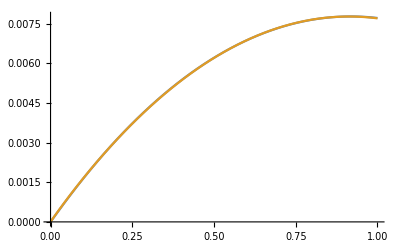

```mathematica
Plot[{(18467/1000000) x^(1.015)+(-10753/1000000) x^(1.876),(0.0168778) x^(0.986014)+(-0.00917692) x^(1.98602)},{x,0,1}]
```

```mathematica
{m=-2,l=3,lp=2,np=0}
```

{-2,3,2,0}

```mathematica
-10753/1000000.
```

-0.010753

```mathematica
(18467/1000000.)
```

0.018467

```mathematica
ModeMixingFitCoeff[0.25,0,0,m,l,lp,np]
```

-0.0402842-0.00932549 ⅈ

```mathematica
re=DiracDelta[l,lp]+(-13475/100000) FinalSpinUIB2017[0.25,0,0]^(1.088)+(7963)/100000 FinalSpinUIB2017[0.25,0,0]^(1.279)
im=(-1744/100000) FinalSpinUIB2017[0.25,0,0]^(1.011)+(516/100000) FinalSpinUIB2017[0.25,0,0]^(1.821)
```

-0.0402676

-0.00932055

```mathematica
sxsdir="/Users/xisco/SXS";
sxsdirs=Select[FileNames["*",sxsdir],DirectoryQ[#]&];
```

```mathematica
mysxscase=SXSParClassification[sxsdirs,{{"Non-Precessing"},{"MassRatio","3.9<#<4.1"},{"χ1","#<0.9"},{"χ2","#<0.9"}}][[1]]
modes={{2,2},{2,1},{3,2},{3,3},{4,3},{4,4}}
```

Classification Input Variables. Examples: {{'MassRatio', '0.99<#<1.1'}},{{'Distance', '#>16'}},{{'Orbits', '#>25'}},{{'Precessing'}},
{{'Non-Precessing'}},{{'High-Spin'}},{{'χeff','#>0.6'}},{{'χ1','#>0.6'}},{{'χ2','#>0.6'}},{{'Unequal'}}

Take care! Some of the sxs file names are not consistent with the metadata files

The spin definition is consitent with 'initial-spin' values and not relaxed ones

The mass definition is consitent with 'initial-mass' values and not relaxed ones

/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0

{{2,2},{2,1},{3,2},{3,3},{4,3},{4,4}}

```mathematica
mysxscaserh=Reverse[Select[FileNames["*rM*",mysxscase,2],Not@StringMatchQ[#,"*raw*"]&]][[1;;1]]
mysxscasemetafile=FileNames["metadata.txt",mysxscase,2][[1]]
metadata=SXSMetaFilesToRules[mysxscasemetafile];
```

{/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0/Lev4/rMPsi4_Asymptotic_GeometricUnits_CoM.h5}

/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0/Lev2/metadata.txt

```mathematica
mysxscasemetadata=SXSMetaFilesToRules[mysxscasemetafile];
Print["mass1 = ",mass1=("initial-mass1"/.metadata)[[1]]]
Print["mass2 = ",mass2=("initial-mass2"/.metadata)[[1]]]
Print["χ1 = ",χ1=Chop[(("initial-dimensionless-spin1"/.metadata)[[-1]])]]
Print["χ2 = ",χ2=Chop[(("initial-dimensionless-spin2"/.metadata)[[-1]])]]
Print["m1/m2 = ",q=Max[{mass1/mass2,1}]]
Print["m1·m2 = ",η=q/(1+q)^2*1.]
Print["af = ",af=("remnant-dimensionless-spin"/.metadata)[[-1]]]
Print["mf = ",mf=("remnant-mass"/.metadata)[[1]]]
```

mass1 = 0.8

mass2 = 0.2

χ1 = -1.7059×10^-9

χ2 = -1.64615×10^-8

m1/m2 = 4.

m1·m2 = 0.16

af = 0.471805

mf = 0.977701

```mathematica
sxsrhs=Flatten[Conjugate/@GetAsymptoticMultiMode[#,2,modes,"ReSample"->True]&/@mysxscaserh,1];
```

```mathematica
tmax=TimeOfMaximum[sxsrhs[[1]]]
```

7201.71

```mathematica
mu2320=ModeMixingFitCoeff[η,χ1,χ2,2,3,2,0]
mu2220=ModeMixingFitCoeff[η,χ1,χ2,2,2,2,0]
mu2330=ModeMixingFitCoeff[η,χ1,χ2,2,3,3,0]
```

ModeMixingFitCoeff[0.16,-1.7059×10^-9,-1.64615×10^-8,2,3,2,0]

ModeMixingFitCoeff[0.16,-1.7059×10^-9,-1.64615×10^-8,2,2,2,0]

ModeMixingFitCoeff[0.16,-1.7059×10^-9,-1.64615×10^-8,2,3,3,0]

```mathematica
mu3430=ModeMixingFitCoeff[η,χ1,χ2,3,4,3,0]
mu3330=ModeMixingFitCoeff[η,χ1,χ2,3,3,3,0]
mu3440=ModeMixingFitCoeff[η,χ1,χ2,3,4,4,0]
```

-0.0523296-0.00587438 ⅈ

-0.00132368-0.00896474 ⅈ

-0.00485412-0.022675 ⅈ

```mathematica
mu2320n=ModeMixingFitCoeffSYNorm[η,χ1,χ2,2,3,2,0,0]
mu2220n=ModeMixingFitCoeffSYNorm[η,χ1,χ2,2,2,2,0,0]
mu2330n=ModeMixingFitCoeffSYNorm[η,χ1,χ2,2,3,3,0,0]
```

-0.231359-0.12649 ⅈ

-0.000843381+0.00612128 ⅈ

-0.00404487-0.0161968 ⅈ

```mathematica
mu3430n=ModeMixingFitCoeffSYNorm[η,χ1,χ2,3,4,3,0,0]
mu3330n=ModeMixingFitCoeffSYNorm[η,χ1,χ2,3,3,3,0,0]
mu3440n=ModeMixingFitCoeffSYNorm[η,χ1,χ2,3,4,4,0,0]
```

-0.332692-0.162145 ⅈ

-0.00132368-0.00896474 ⅈ

-0.00485412-0.022675 ⅈ

```mathematica
h320unmf=Transpose[{sxsrhs[[3,All,1]],(sxsrhs[[3,All,2]]-sxsrhs[[1,All,2]](Conjugate[mu2320]/Conjugate[mu2220]))/mu2330}];
```

```mathematica
h430unmf=Transpose[{sxsrhs[[3,All,1]],1/mu3440(sxsrhs[[5,All,2]]-sxsrhs[[4,All,2]](mu3430/mu3330))}];
```

```mathematica
h320unmfv2=Transpose[{sxsrhs[[3,All,1]],(sxsrhs[[3,All,2]]-sxsrhs[[1,All,2]](Conjugate[mu2320n]/Conjugate[mu2220n]))/mu2330n}];
```

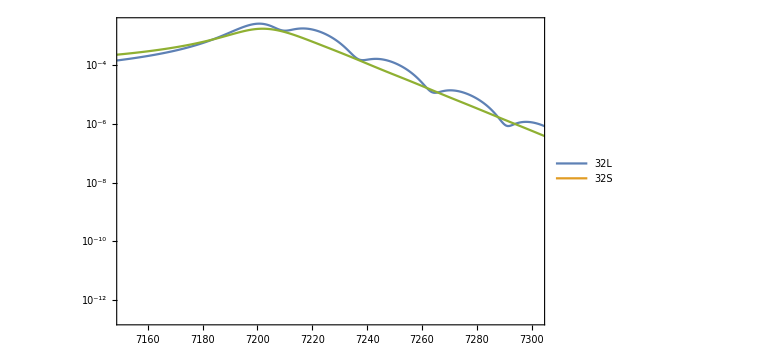

```mathematica
ListLogPlot[{Abs0DStructs@sxsrhs[[3]],Abs0DStructs@h320unmf,(Abs0DStructs@h320unmfv2)/.{xx_,yy_}->{xx,yy/50000}},PlotRange->{{tmax-100,tmax+100},All},Joined->True,Frame->True,ImageSize->Large,PlotLegends->{"32L","32S"}]
```

```mathematica
freq1=D[(Interpolation[Arg0DStructs@sxsrhs[[3]]])@t,t]
```

InterpolatingFunction[…][t]

```mathematica
freq2=D[(Interpolation[(Arg0DStructs@h320unmfv2)])@t,t]
```

InterpolatingFunction[…][t]

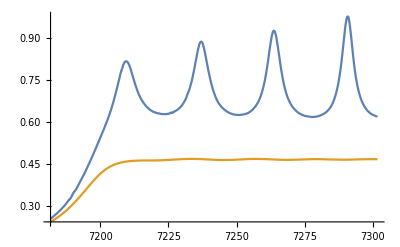

```mathematica
Plot[{freq1,freq2},{t,tmax-20,tmax+100}]
```

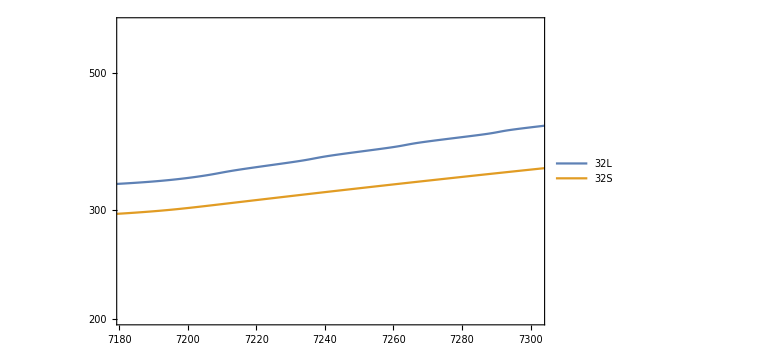

```mathematica
ListLogPlot[{Arg0DStructs@sxsrhs[[3]],(Arg0DStructs@h320unmfv2)},PlotRange->{{tmax-20,tmax+100},{200,600}},Joined->True,Frame->True,ImageSize->Large,PlotLegends->{"32L","32S"}]
```

```mathematica
ValueOfMaximum[h430unmf]/100
```

0.151718

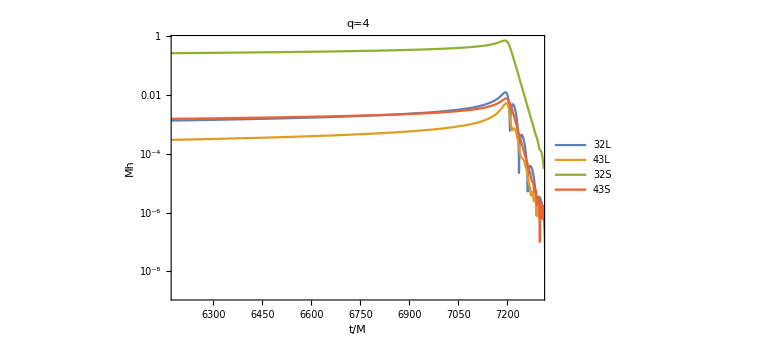

```mathematica
ListLogPlot[{Abs0DStructs@sxsrhs[[3]],Abs0DStructs@sxsrhs[[5]],Abs0DStructs[h320unmf]/.{xx_,yy_}->{xx,yy/140},Abs0DStructs[h430unmf]/.{xx_,yy_}->{xx,yy/2000}},PlotRange->{{tmax-1000,tmax+100},Automatic},Joined->True,Frame->True,ImageSize->Large,PlotLegends->Placed[{"32L","43L","32S","43S"},{0.1,0.2}],FrameStyle->Directive[Black,Bold,16],FrameLabel->{"t/M","Mh"},PlotLabel->"q=4",LabelStyle->Directive[Black,Bold,16]]
```

```mathematica
modes
```

{{2,2},{2,1},{3,2},{3,3},{4,3},{4,4}}

```mathematica
Abs[mu3430/mu3330]
```

5.81093

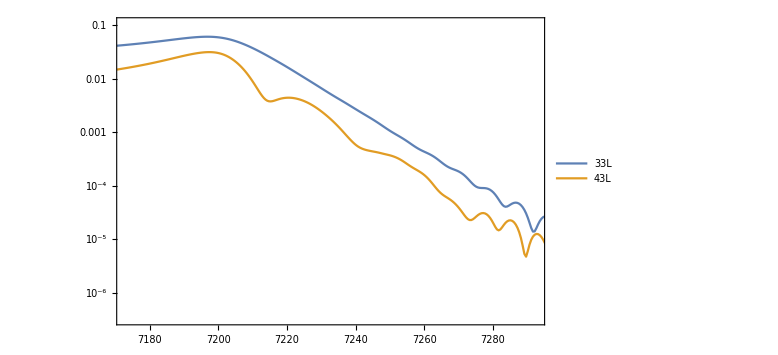

```mathematica
ListLogPlot[{Abs0DStructs@sxsrhs[[4]],Abs0DStructs@sxsrhs[[5]]/.{xx_,yy_}->{xx,yy*6}},PlotRange->{{tmax-20,tmax+100},All},Joined->True,Frame->True,ImageSize->Large,PlotLegends->{"33L","43L"}]
```